```mathematica
filename="E:\\Research_Tool\\My_Project\\data_process\\RRR\\RRR.xlsx";afirst=Import[filename];
a=Table[afirst[[1,i]],{i,1,Length[afirst[[1]]]}];
a11=Table[{a[[i,1]],a[[i,2]]},{i,1,Length[afirst[[1]]]}];
a12=Table[{a[[i,1]],a[[i,3]]},{i,1,Length[afirst[[1]]]}];
a21=Table[{a[[i,4]],a[[i,5]]},{i,1,Length[afirst[[1]]]}];
a22=Table[{a[[i,4]],a[[i,6]]},{i,1,Length[afirst[[1]]]}];
afilter=a11;
ax=Table[afilter[[i,1]],{i,1,Length[afilter]}];ay=Table[afilter[[i,2]],{i,1,Length[afilter]}];
minay=Min[ay];ay=ay-minay;
Fay=Fourier[ay];
Min[ay]-Max[ay]
```

-1.8815×10^-8

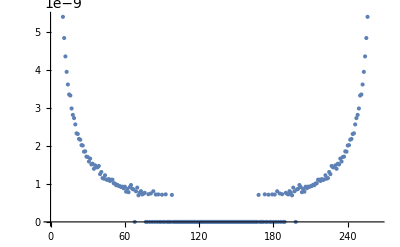

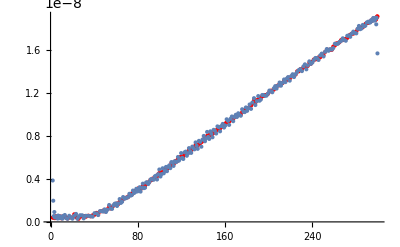

```mathematica
PFay=Table[If[Abs[Fay[[i]]]<0.7*10^-9,0,Fay[[i]]],{i,1,Length[a]}];
ListPlot[Abs[PFay]]
ListFlatteny=Abs[InverseFourier[PFay]];
ListFlatten=Table[{ax[[i]],ListFlatteny[[i]]+minay},{i,1,Length[a]}];
Show[ListPlot[afilter,PlotStyle->Red],ListPlot[ListFlatten],ImageSize->Full]
```

```mathematica
Export["E:\\Research_Tool\\My_Project\\data_process\\9cell5\\20230613_6_Fourier_filter_data.csv",ListFlatten]
```

E:\Research_Tool\My_Project\data_process\9cell5\20230613_6_Fourier_filter_data.csv

{}

```mathematica
fitarray=a21;
```

```mathematica
fitT5={};For[i=1,i≤Length[fitarray],i++,If[fitarray[[i,2]]<1*10^-9,fitT5=Insert[fitT5,fitarray[[i]],-1]]]
```

```mathematica
FindFit[fitT5,a0+a5*T^5,{a0,a5},T]
```

{a0→9.15701×10^-11,a5→1.93242×10^-18}

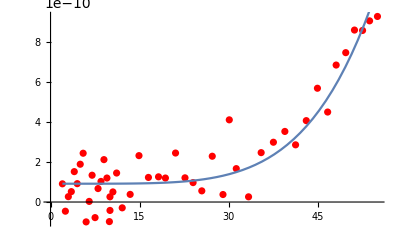

```mathematica
Show[ListPlot[fitT5,PlotStyle->Red],Plot[a0+a5 T^5/.{a0->9.15701040341593*^-11,a5->1.9324175582078658*^-18},{T,1.99985,55.0709}]]
```

```mathematica
fitT1={};For[i=1,i≤Length[fitarray],i++,If[fitarray[[i,2]]>1*10^-9,fitT1=Insert[fitT1,fitarray[[i]],-1]]]
```

```mathematica
FindFit[fitT1,a0+a1*T,{a0,a1},T]
```

{a0→-3.02542×10^-9,a1→7.00249×10^-11}

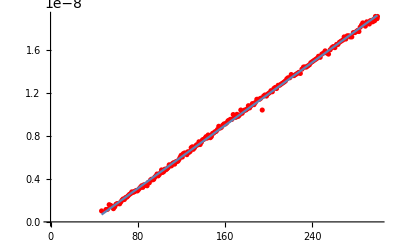

```mathematica
Show[ListPlot[fitT1,PlotStyle->Red],Plot[a0+a1 T/.{a0->-2.748174143252613*^-9,a1->7.320641080372363*^-11},{T,46.8261,299.96225}]]
```

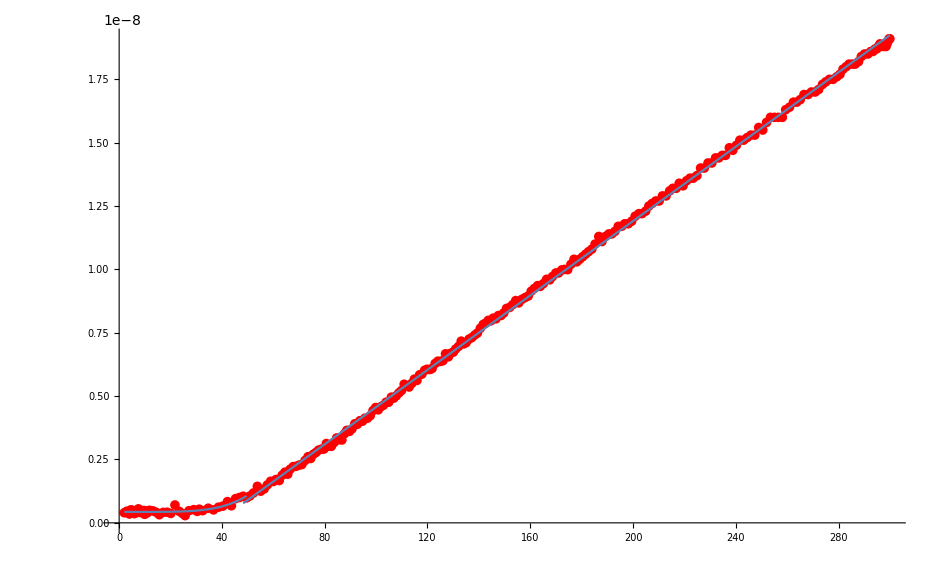

```mathematica
Show[ListPlot[a11,PlotStyle->Red],Plot[a0+a1 T/.{a0->-2.770759048831692*^-9,a1->7.339176161986901*^-11},{T,48.26855,299.96225}],Plot[a0+a5 T^5/.{a0->4.314925925422196*^-10,a5->2.1048569296496734*^-18},{T,1.99995,49.58455}]]
```